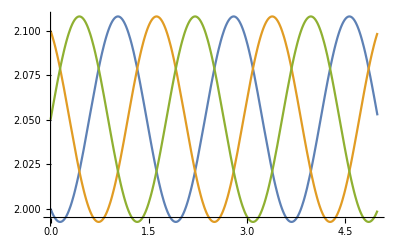

```mathematica
sol=NDSolve[{
x'[t]==(+x[t]-x[t]*y[t])+(-x[t]+x[t]*z[t]),
y'[t]==(-y[t]+x[t]*y[t])+(y[t]-y[t]*z[t]),
z'[t]==(+z[t]-x[t]*z[t])+(-z[t]+y[t]*z[t]),
{x[0],y[0],z[0]}=={2,2.1,2.05}},{x[t],y[t],z[t]},{t,0,5}];
xs=(x[t]/.sol)[[1]];
ys=(y[t]/.sol)[[1]];
zs=(z[t]/.sol)[[1]];
Plot[{xs,ys,zs},{t,0,5}]
```

```mathematica
expr//MatrixForm//TraditionalForm
{x'[t]==(+x[t]-x[t]*y[t])+(-x[t]+x[t]*z[t]),
y'[t]==(-y[t]+x[t]*y[t])+(y[t]-y[t]*z[t]),
z'[t]==(+z[t]-x[t]*z[t])+(-z[t]+y[t]*z[t])}/.{x->a,y->b,z->c}//MatrixForm//TraditionalForm
```

(a'(t)==a(t) c(t)-a(t) b(t)
b'(t)==a(t) b(t)-b(t) c(t)
c'(t)==b(t) c(t)-a(t) c(t))

(a'(t)==a(t) c(t)-a(t) b(t)
b'(t)==a(t) b(t)-b(t) c(t)
c'(t)==b(t) c(t)-a(t) c(t))

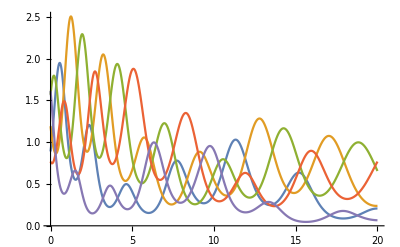

```mathematica
n=5;
tmax=20;
Mat=RandomReal[{0.8,1.3},{n,n}];
Letters=FromCharacterCode[#]&/@Range[97,97+n];
expr=Table[subN=i;Symbol[Letters[[i]]]'[t]==Sum[If[i==j,0,subN++;(Symbol[Letters[[i]]][t]*(-1)^subN+(-1)^(subN+1)*(Mat[[i,j]]*Symbol[Letters[[i]]][t]*Symbol[Letters[[j]]][t]))],{j,1,n}],{i,1,n}];
startExpr=Table[Symbol[Letters[[i]]][0]==RandomReal[{0.5,2}],{i,1,n}];
solvExpr=Table[Symbol[Letters[[i]]][t],{i,1,n}];
inputExpr=Flatten[{expr,startExpr}];
sol=NDSolve[inputExpr,
solvExpr,{t,0,tmax}];
s=Table[(Symbol[Letters[[i]]][t]/.sol)[[1]],{i,1,n}];
Plot[s,{t,0,tmax},PlotRange->{All,{0,All}}]
```

```mathematica
bwidth=1.5;
Animate[Plot[Evaluate[s],{t,Max[0,ct-bwidth],ct},PlotRange->{{Max[0,ct-bwidth],ct},{0,2.6}},PlotTheme->"Scientific",Filling->Axis,ImageSize->Large,FrameLabel->{"Time t","Populations ℼ(n)"},Epilog->Inset[Framed[LineLegend[ColorData[97]/@Range[1,5],Table["Population ℼ("<>ToString[i]<>")",{i,1,5}]],Background->Opacity[0.5,White]],{ct-1.2*bwidth/5,2.5},{Left,Top}],FrameTicks->{{Automatic,Automatic},{Table[i,{i,Ceiling[Max[0,ct-bwidth]*10]/10+0.03,ct-0.03,0.1}],None}}],{ct,bwidth,tmax},AnimationRate->.2]
```

```mathematica
bwidth=1.5;
imgs=Table[Plot[Evaluate[s],{t,Max[0,ct-bwidth],ct},PlotRange->{{Max[0,ct-bwidth],ct},{0,2.6}},PlotTheme->"Scientific",Filling->Axis,ImageSize->Large,FrameLabel->{"Time t","Populations ℼ(n)"},Epilog->Inset[Framed[LineLegend[ColorData[97]/@Range[1,5],Table["Population ℼ("<>ToString[i]<>")",{i,1,5}]],Background->Opacity[0.5,White]],{ct-1.2*bwidth/5,2.5},{Left,Top}],FrameTicks->{{Automatic,Automatic},{Table[i,{i,Ceiling[Max[0,ct-bwidth]*10]/10+0.03,ct-0.03,0.1}],None}}],{ct,bwidth,tmax,0.025}];
```

```mathematica
Export[NotebookDirectory[]<>"multiplePredatorPreyModel.gif",imgs,"DisplayDurations"->0.1]
```

C:\Users\Julien\Desktop\Science Animations\MultiplePredatorHunterModel\multiplePredatorPreyModel.gif